# Hints for a luminosity transition in the Cepheid SnIa calibrator data Leandros Perivolaropoulos and Foteini Skara The one dimensional relative probability density value of H0 for all cases studied. All measurements are shown as normalized Gaussian distribution

```mathematica
op=0.003;
thib=0.003;
thi=0.004;
```

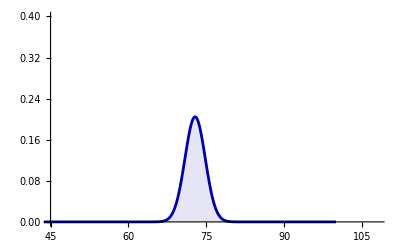

```mathematica
hoss=Plot[PDF[NormalDistribution[72.86,1.95],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Thickness[0.005],Darker[Blue]},FillingStyle->Directive[Opacity[0.1]],Filling->Axis]
```

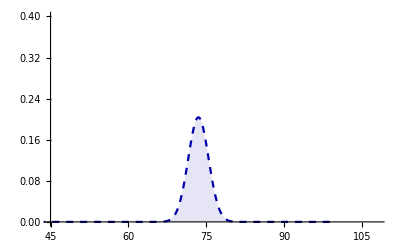

```mathematica
hossb=Plot[PDF[NormalDistribution[73.50,1.96],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Dashed,Thickness[0.004],Darker[Blue]},FillingStyle->Directive[Opacity[0.1]],Filling->Axis]
```

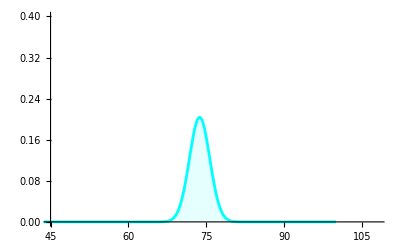

```mathematica
hos=Plot[PDF[NormalDistribution[73.73,1.96],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Thickness[0.005],Cyan},FillingStyle->Directive[Opacity[0.1]],Filling->Axis]
```

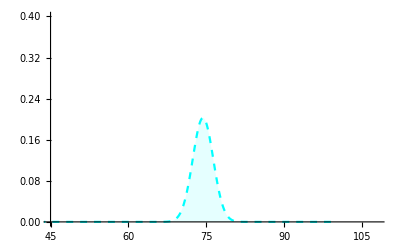

```mathematica
hosb=Plot[PDF[NormalDistribution[74.38,1.97],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Dashed,Thickness[0.004],Cyan},FillingStyle->Directive[Opacity[0.1]],Filling->Axis]
```

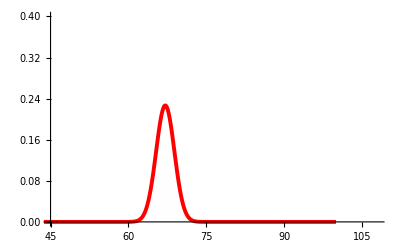

```mathematica
hoi=Plot[PDF[NormalDistribution[67.11,1.76],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Thickness[thi+0.003],Red},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

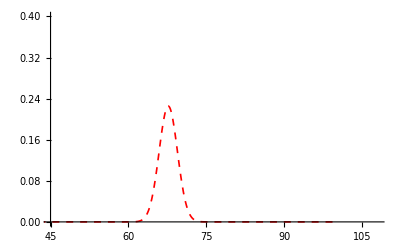

```mathematica
hoib=Plot[PDF[NormalDistribution[67.69,1.77],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Dashed,Thickness[thib],Red},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

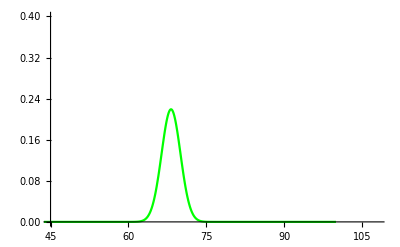

```mathematica
hoii=Plot[PDF[NormalDistribution[68.22,1.82],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Thickness[thi],Green},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

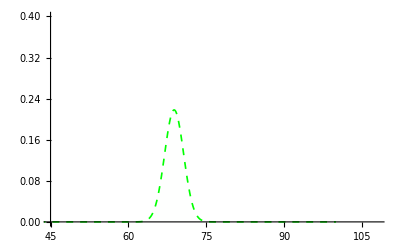

```mathematica
hoiib=Plot[PDF[NormalDistribution[68.82,1.83],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Dashed,Thickness[thib],Green},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

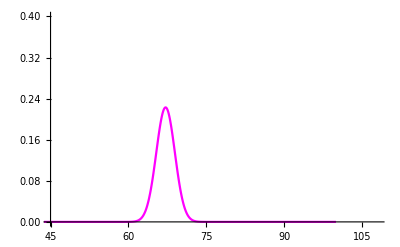

```mathematica
hoiii=Plot[PDF[NormalDistribution[67.17,1.79],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Thickness[thi],Magenta},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

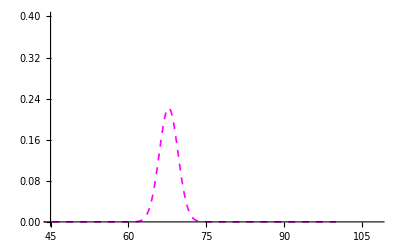

```mathematica
hoiiib=Plot[PDF[NormalDistribution[67.76,1.80],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Dashed,Thickness[thib],Magenta},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

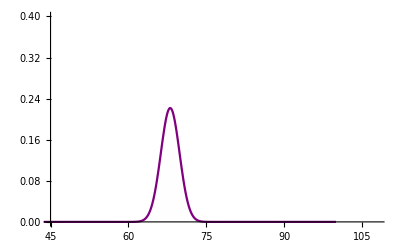

```mathematica
hoiv=Plot[PDF[NormalDistribution[68.06,1.80],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Thickness[thi],Purple},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

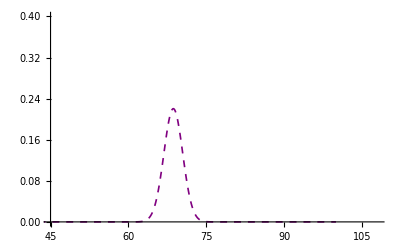

```mathematica
hoivb=Plot[PDF[NormalDistribution[68.66,1.81],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Dashed,Thickness[thib],Purple},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

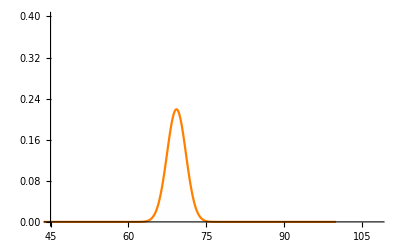

```mathematica
hov=Plot[PDF[NormalDistribution[69.27,1.82],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Thickness[thi],Orange},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

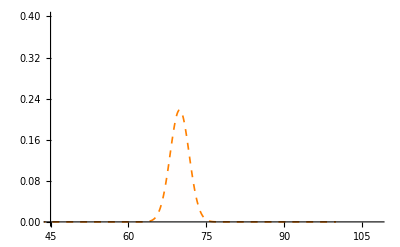

```mathematica
hovb=Plot[PDF[NormalDistribution[69.88,1.83],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Dashed,Thickness[thib],Orange},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

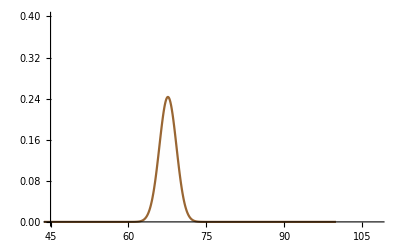

```mathematica
hovi=Plot[PDF[NormalDistribution[67.62,1.64],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Thickness[thi],Brown},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

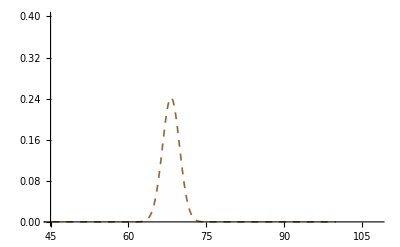

```mathematica
hovib=Plot[PDF[NormalDistribution[68.22,1.65],x],{x,40,100},PlotRange->{{45,108},{0,0.4}},PlotStyle->{PointSize->Large,Dashed,Thickness[thib],Brown},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

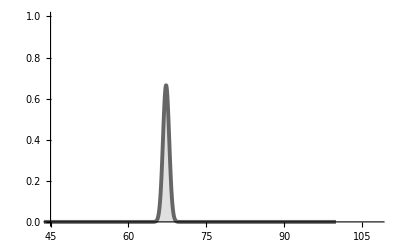

```mathematica
pl18=Plot[PDF[NormalDistribution[67.27,0.6],x],{x,40,100},PlotRange->{{45,108},{0,1}},PlotStyle->{PointSize->Large,Thickness[0.007],RGBColor[0.4,0.4,0.4]},Filling->Axis]
```

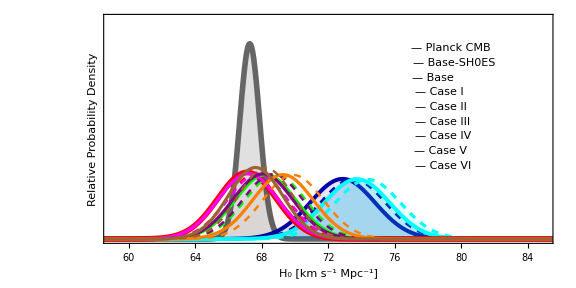

```mathematica
figprh0=Show[pl18,hoss,hossb,hos,hosb,hoi,hoib,hoii,hoiib,hoiii,hoiiib,hoiv,hoivb,hov,hovb,hovi,hovib,Graphics[{Inset["— Planck CMB",{79.4,0.65},BaseStyle->{Bold,RGBColor[0.4,0.4,0.4],FontFamily->"Times",14}]}],Graphics[{Inset["— Base-SH0ES ",{79.55,0.6},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],
Graphics[{Inset["— Base ",{78.3,0.55},BaseStyle->{Bold,Cyan,FontFamily->"Times",14}]}],
Graphics[{Inset["— Case I ",{78.68,0.5},BaseStyle->{Bold,Red,FontFamily->"Times",14}]}],
Graphics[{Inset["— Case II ",{78.8,0.45},BaseStyle->{Bold,Green,FontFamily->"Times",14}]}],
Graphics[{Inset["— Case III ",{78.9,0.4},BaseStyle->{Bold,Magenta,FontFamily->"Times",14}]}],
Graphics[{Inset["— Case IV ",{78.9,0.35},BaseStyle->{Bold,Purple,FontFamily->"Times",14}]}],
Graphics[{Inset["— Case V ",{78.75,0.3},BaseStyle->{Bold,Orange,FontFamily->"Times",14}]}],Graphics[{Inset["— Case VI ",{78.9,0.25},BaseStyle->{Bold,Brown,FontFamily->"Times",14}]}],
PlotRange->{{59,85},{0,0.75}},LabelStyle->Directive[Bold,Italic,18,Black],FrameLabel->{"H_0   [km s^-1 Mpc^-1]  ","Relative Probability Density"},Frame->True,BaseStyle->{FontFamily->"Times",8},FrameStyle->Directive[Black,Thickness[0.007]],FrameTicks->{{None,None},{All,None}},AspectRatio->0.5,ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figprh0.pdf",figprh0,ImageResolution->1000];
```